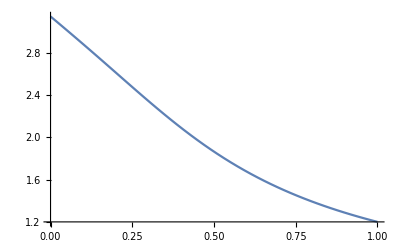

```mathematica
Subscript[α, m][x_]:=π-ArcTan[1/(√(4/(27 x^2)-1+x))]/;0<x<=2/3
Subscript[α, m][x_]:=ArcTan[1/(√(4/(27 x^2)-1+x))]/;2/3<x<1
Plot[Subscript[α, m][x],{x,0,1}]
```

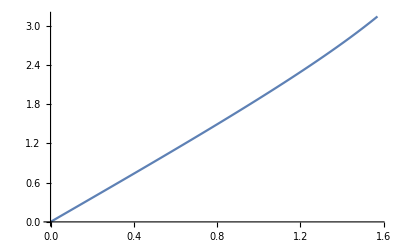

```mathematica
Subscript[ψ, m][x_]:=π-ArcSin[x √((27(1-x))/4)]/;0<x<=2/3
Subscript[ψ, m][x_]:=ArcSin[x √((27(1-x))/4)]/;2/3<x<1
Plot[Subscript[ψ, m][Cos[x]],{x,0,π/2}]
```

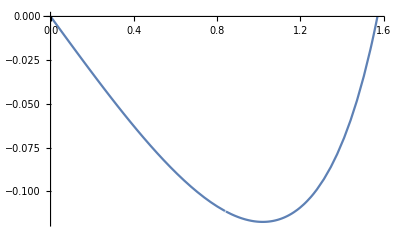

```mathematica
Plot[Subscript[ψ, m][Cos[x]]-2x,{x,0,π/2}]
```

```mathematica
num=64;
alphaMTable=Table[Subscript[α, m][0.9999(i-1)/(num-1)],{i,1,num}];
alphaMTable[[1]]=N[π];
Export["E:\\files\\C++\\BlackHoleRendering\\BlackHoleRendering\\BlackHoleRenderingNoneCuda\\resources\\alpha_m.txt",alphaMTable,"Table"];
alphaMTable
```

{3.14159,3.10035,3.05904,3.01761,2.97604,2.93428,2.89233,2.85017,2.8078,2.76525,2.72254,2.67969,2.63675,2.59376,2.55078,2.50787,2.46509,2.42252,2.38021,2.33824,2.29668,2.2556,2.21506,2.17512,2.13584,2.09727,2.05944,2.02241,1.98621,1.95085,1.91636,1.88276,1.85004,1.81823,1.78731,1.75727,1.72812,1.69984,1.67242,1.64583,1.62006,1.59509,1.5709,1.54746,1.52476,1.50276,1.48146,1.46081,1.44081,1.42143,1.40264,1.38442,1.36676,1.34963,1.33301,1.31688,1.30123,1.28603,1.27127,1.25693,1.24299,1.22944,1.21627,1.20345}

```mathematica
num=64;
psiMTable=Table[N[Subscript[ψ, m][0.9999Cos[(π(i-1))/(2(num-1))]]],{i,1,num}];(*0.9999是为了和后面求偏转角相对应, Subscript[那里u, a] 不能等于1*)
psiMTable[[num]]=N[π];
Export["E:\\files\\C++\\BlackHoleRendering\\BlackHoleRendering\\BlackHoleRenderingNoneCuda\\resources\\psi_m_cos_t.txt",psiMTable,"Table"];
psiMTable
```

{0.0259811,0.0526602,0.095226,0.139863,0.185087,0.230564,0.276179,0.321884,0.367658,0.413491,0.459376,0.505314,0.551303,0.597345,0.643443,0.6896,0.735818,0.782102,0.828456,0.874883,0.921389,0.967978,1.01466,1.06143,1.1083,1.15527,1.20236,1.24956,1.29689,1.34434,1.39194,1.43968,1.48758,1.53564,1.58388,1.63229,1.6809,1.72972,1.77874,1.828,1.8775,1.92726,1.97729,2.02761,2.07824,2.12919,2.18049,2.23216,2.28423,2.33673,2.38967,2.44311,2.49707,2.5516,2.60674,2.66254,2.71905,2.77636,2.83451,2.89361,2.95375,3.01503,3.0776,3.14159}

```mathematica
num=64;
data=Table[Table[0,{j,1,num}],{i,1,num}];
root=5.5;
For[i=2,i<num+1,i++,
Clear[y];
u0=N[(0.9999 (i-1))/(num-1)];
Subscript[α, mu]=Subscript[α, m][u0];
sol=NDSolve[{y''[x]+y[x]-3/2 y[x]^2==0,y[0]==u0,y'[0]==-u0 Cot[0.999 Subscript[α, mu]]},y,{x,0,18}];
t=y/.sol[[1,1]];
root=x/.FindRoot[t[x],{x,root}][[1]];
data[[i,num]]=root;
root1=root*0.7;(*我也不知道为啥0.7这么好*)
For[j=num-1,j>1,j--,
Clear[y];
sol=NDSolve[{y''[x]+y[x]-3/2 y[x]^2==0,y[0]==u0,y'[0]==-u0 Cot[0.999((j-1) Subscript[α, mu])/(num-1)]},y,{x,0,18}];
t=y/.sol[[1,1]];
root1=x/.FindRoot[t[x],{x,root1 j/(j+1)}][[1]];
data[[i,j]]=root1;
];
]
```

```mathematica
Export["E:\\files\\C++\\BlackHoleRendering\\BlackHoleRendering\\BlackHoleRenderingNoneCuda\\resources\\unified.txt",data,"Table"]
```

E:\files\C++\BlackHoleRendering\BlackHoleRendering\BlackHoleRenderingNoneCuda\resources\unified.txt

```mathematica
data
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0.0491633,0.0983309,0.147507,0.196695,0.245901,0.295126,0.344376,0.393654,0.442963,0.492307,0.541688,0.591108,0.640572,0.690079,0.739633,0.789233,0.838883,0.888581,0.93833,0.988128,1.03798,1.08787,1.13782,1.18782,1.23786,1.28795,1.33808,1.38826,1.43848,1.48874,1.53904,1.58938,1.63977,1.69019,1.74066,1.79117,1.84173,1.89234,1.943,1.99373,2.04453,2.09542,2.1464,2.1975,2.24874,2.30015,2.35177,2.40364,2.45583,2.50841,2.56149,2.61521,2.66977,2.72546,2.78267,2.84206,2.90465,2.97224,3.04827,3.14025,3.26837,3.51325,5.42637},{0,0.0485089,0.097026,0.145559,0.194117,0.242706,0.291335,0.340011,0.388741,0.437531,0.486388,0.535318,0.584325,0.633415,0.682591,0.731858,0.781218,0.830673,0.880226,0.929878,0.97963,1.02948,1.07943,1.12948,1.17963,1.22987,1.2802,1.33063,1.38115,1.43175,1.48244,1.53322,1.58408,1.63502,1.68605,1.73716,1.78836,1.83966,1.89106,1.94257,1.99421,2.04599,2.09793,2.15007,2.20243,2.25506,2.30802,2.36137,2.4152,2.46963,2.5248,2.5809,2.6382,2.69705,2.75795,2.82164,2.88923,2.9625,3.04448,3.14081,3.26336,3.44242,3.78889,6.03059},{0,0.0478527,0.0957171,0.143605,0.191528,0.239496,0.287522,0.335616,0.383788,0.432047,0.480403,0.528865,0.57744,0.626136,0.674959,0.723914,0.773007,0.822241,0.87162,0.921145,0.97082,1.02064,1.07062,1.12074,1.171,1.22142,1.27197,1.32267,1.3735,1.42447,1.47557,1.5268,1.57817,1.62965,1.68127,1.73302,1.78491,1.83694,1.88913,1.94148,1.99402,2.04678,2.09977,2.15305,2.20665,2.26064,2.3151,2.37013,2.42584,2.4824,2.54001,2.59894,2.65953,2.72229,2.78789,2.85731,2.93205,3.01441,3.10833,3.22092,3.36679,3.58199,3.99209,6.38824},{0,0.047194,0.0944029,0.141642,0.188925,0.236268,0.283684,0.331187,0.37879,0.426506,0.474347,0.522324,0.570449,0.618729,0.667175,0.715793,0.764592,0.813576,0.86275,0.912118,0.961683,1.01145,1.06141,1.11157,1.16193,1.21248,1.26322,1.31416,1.36528,1.41659,1.46808,1.51975,1.57159,1.62361,1.67581,1.72818,1.78075,1.8335,1.88647,1.93966,1.9931,2.04682,2.10085,2.15525,2.21008,2.26541,2.32134,2.37799,2.43552,2.49411,2.55403,2.6156,2.67926,2.74561,2.81548,2.89004,2.97106,3.0613,3.16532,3.29127,3.45562,3.69796,4.15214,6.64022},{0,0.0465323,0.0930826,0.139669,0.186308,0.233019,0.279818,0.326721,0.373745,0.420905,0.468216,0.515692,0.563346,0.61119,0.659235,0.707491,0.755968,0.804672,0.85361,0.902788,0.95221,1.00188,1.05179,1.10196,1.15237,1.20303,1.25393,1.30507,1.35646,1.40807,1.45992,1.512,1.5643,1.61683,1.66959,1.72258,1.7758,1.82927,1.88301,1.93703,1.99136,2.04603,2.1011,2.15661,2.21264,2.26928,2.32665,2.38488,2.44415,2.5047,2.56682,2.63089,2.69742,2.7671,2.84086,2.92007,3.0067,3.10384,3.21654,3.35372,3.53312,3.7967,4.28343,6.83318},{0,0.0458675,0.0917556,0.137685,0.183676,0.229748,0.275922,0.322217,0.368651,0.415243,0.462009,0.508966,0.556131,0.603516,0.651137,0.699005,0.747131,0.795525,0.844196,0.89315,0.942393,0.99193,1.04176,1.09189,1.14232,1.19305,1.24407,1.29539,1.34699,1.39889,1.45106,1.50352,1.55626,1.60928,1.66257,1.71615,1.77002,1.82419,1.87868,1.93352,1.98872,2.04434,2.10042,2.15703,2.21425,2.27218,2.33095,2.39071,2.45168,2.51412,2.57834,2.64478,2.714,2.78678,2.86414,2.94758,3.03926,3.14252,3.26278,3.40955,3.60149,3.88221,4.39409,6.98837},{0,0.0451993,0.0904217,0.13569,0.181027,0.226456,0.271998,0.317675,0.363508,0.409519,0.455725,0.502148,0.548803,0.59571,0.642882,0.690335,0.738083,0.786136,0.834506,0.883202,0.932231,0.981599,1.03131,1.08137,1.13178,1.18253,1.23363,1.28508,1.33688,1.38901,1.44148,1.49429,1.54743,1.6009,1.65471,1.70885,1.76335,1.8182,1.87343,1.92906,1.98513,2.04167,2.09876,2.15644,2.21483,2.27402,2.33416,2.39543,2.45804,2.52229,2.58853,2.65722,2.729,2.80467,2.88537,2.97269,3.06895,3.17769,3.30463,3.4597,3.66228,3.95716,4.48912,7.11722},{0,0.0445279,0.0890811,0.133684,0.178363,0.223142,0.268045,0.313096,0.358318,0.403735,0.449368,0.495238,0.541367,0.587772,0.634473,0.681485,0.728825,0.776508,0.824544,0.872947,0.921725,0.970886,1.02044,1.07038,1.12072,1.17147,1.22261,1.27415,1.32609,1.37842,1.43115,1.48426,1.53777,1.59167,1.64596,1.70064,1.75573,1.81124,1.86718,1.92359,1.9805,2.03796,2.09602,2.15477,2.2143,2.27473,2.33621,2.39894,2.46315,2.52915,2.59733,2.66818,2.74237,2.82077,2.90458,2.99549,3.09593,3.20962,3.3425,3.50486,3.7166,4.02341,4.57181,7.22655},{0,0.0438535,0.0877341,0.131669,0.175684,0.219807,0.264064,0.308481,0.353083,0.397894,0.44294,0.488243,0.533825,0.579709,0.625915,0.672461,0.719366,0.766647,0.814317,0.862391,0.910881,0.959796,1.00914,1.05893,1.10917,1.15985,1.21099,1.26258,1.31462,1.36711,1.42005,1.47343,1.52727,1.58155,1.63628,1.69147,1.74713,1.80326,1.85989,1.91706,1.97478,2.03313,2.09215,2.15194,2.21258,2.27422,2.33702,2.40117,2.46693,2.53463,2.60467,2.67759,2.75407,2.83505,2.92178,3.01602,3.12031,3.2385,3.37672,3.54554,3.76526,4.08228,4.64444,7.32073},{0,0.0431764,0.0863816,0.129644,0.172993,0.216455,0.26006,0.303834,0.347806,0.392001,0.436446,0.481166,0.526186,0.571528,0.617217,0.663272,0.709714,0.756563,0.803835,0.851546,0.89971,0.94834,0.997446,1.04704,1.09712,1.1477,1.19879,1.25037,1.30247,1.35507,1.40817,1.46179,1.5159,1.57053,1.62567,1.68132,1.7375,1.79423,1.85152,1.9094,1.96792,2.02713,2.08708,2.14788,2.20962,2.27244,2.33651,2.40205,2.46932,2.53866,2.6105,2.68539,2.76407,2.84749,2.93696,3.03431,3.14216,3.26446,3.40752,3.58211,3.80888,4.13475,4.70859,7.40273},{0,0.0424972,0.0850246,0.127612,0.17029,0.213087,0.256034,0.29916,0.342493,0.386061,0.429894,0.474017,0.518456,0.563239,0.608389,0.653929,0.699882,0.74627,0.793111,0.840425,0.888227,0.936532,0.985353,1.0347,1.08459,1.13502,1.18601,1.23755,1.28964,1.3423,1.39553,1.44932,1.50367,1.55859,1.61409,1.67017,1.72684,1.78412,1.84203,1.9006,1.95987,2.0199,2.08076,2.14253,2.20534,2.26931,2.33462,2.40151,2.47024,2.54116,2.61473,2.69153,2.7723,2.85804,2.9501,3.05035,3.16151,3.28761,3.43507,3.61487,3.84791,4.18154,4.76545,7.47462},{0,0.0418165,0.0836643,0.125575,0.167579,0.209708,0.251992,0.294462,0.337149,0.380082,0.423291,0.466803,0.510648,0.554853,0.599444,0.644446,0.689885,0.735784,0.782164,0.829047,0.87645,0.924392,0.972888,1.02195,1.0716,1.12183,1.17267,1.22411,1.27616,1.32883,1.38212,1.43603,1.49057,1.54574,1.60155,1.658,1.71511,1.7729,1.83138,1.8906,1.95059,2.01142,2.07314,2.13586,2.19969,2.26477,2.33129,2.39948,2.46962,2.54208,2.61733,2.69595,2.77872,2.86666,2.96117,3.06416,3.1784,3.30801,3.45952,3.64404,3.88269,4.2232,4.81588,7.5379},{0,0.041135,0.0823023,0.123534,0.164863,0.20632,0.247938,0.289748,0.331782,0.374072,0.416646,0.459537,0.502773,0.546383,0.590397,0.634841,0.679741,0.725124,0.771014,0.817433,0.864403,0.911944,0.960075,1.00881,1.05817,1.10816,1.15879,1.21009,1.26204,1.31466,1.36796,1.42195,1.47662,1.53198,1.58804,1.64482,1.70232,1.76057,1.81958,1.8794,1.94007,2.00164,2.06419,2.12781,2.19262,2.25878,2.32646,2.39591,2.46742,2.54136,2.61822,2.69859,2.78328,2.87332,2.97015,3.07572,3.19285,3.32572,3.48095,3.66977,3.91351,4.26015,4.86056,7.59369},{0,0.0404536,0.0809403,0.121493,0.162145,0.202929,0.243878,0.285024,0.3264,0.368039,0.409971,0.452229,0.494844,0.537846,0.581265,0.62513,0.66947,0.714313,0.759684,0.80561,0.852113,0.899217,0.946942,0.995308,1.04433,1.09403,1.14442,1.19551,1.24731,1.29984,1.35309,1.40709,1.46183,1.51733,1.57359,1.63064,1.68847,1.74712,1.80662,1.86698,1.92827,1.99055,2.05387,2.11836,2.18411,2.25129,2.3201,2.39076,2.46359,2.53896,2.61736,2.69941,2.78593,2.87799,2.97702,3.08502,3.20486,3.34077,3.49944,3.69222,3.94057,4.29273,4.90001,7.64286},{0,0.0397733,0.0795802,0.119455,0.15943,0.19954,0.239818,0.280297,0.321012,0.361994,0.403277,0.444894,0.486876,0.529256,0.572066,0.615335,0.659095,0.703374,0.748201,0.793604,0.839609,0.886241,0.933523,0.981478,1.03013,1.07949,1.12958,1.18042,1.23201,1.28438,1.33754,1.39149,1.44624,1.50182,1.55822,1.61547,1.67359,1.73259,1.7925,1.85336,1.91522,1.97814,2.0422,2.10749,2.17413,2.2423,2.31217,2.38399,2.45808,2.53482,2.61471,2.69838,2.78665,2.88062,2.98175,3.09206,3.21444,3.35319,3.51506,3.71149,3.96406,4.32121,4.93464,7.68605},{0,0.039095,0.0782242,0.117422,0.156721,0.196158,0.235764,0.275576,0.315625,0.355948,0.396576,0.437544,0.478885,0.520633,0.562819,0.605477,0.648638,0.692333,0.736592,0.781447,0.826924,0.873051,0.919855,0.967361,1.01559,1.06457,1.11432,1.16485,1.21619,1.26835,1.32134,1.37519,1.4299,1.48549,1.54197,1.59937,1.65769,1.71698,1.77725,1.83854,1.90092,1.96443,2.02915,2.0952,2.16268,2.23177,2.30266,2.37559,2.45089,2.52894,2.61025,2.69546,2.78541,2.88121,2.98432,3.09681,3.2216,3.36302,3.52788,3.72768,3.98412,4.34581,4.96478,7.72381},{0,0.0384199,0.0768743,0.115397,0.154024,0.192788,0.231724,0.270867,0.310251,0.349911,0.389881,0.430195,0.470888,0.511994,0.553546,0.595579,0.638125,0.681217,0.724888,0.76917,0.814092,0.859685,0.905977,0.952998,1.00077,1.04932,1.09868,1.14886,1.19989,1.25178,1.30456,1.35825,1.41285,1.46839,1.52489,1.58236,1.64084,1.70034,1.7609,1.82257,1.88539,1.94943,2.01476,2.0815,2.14977,2.21972,2.29157,2.36555,2.442,2.5213,2.60397,2.69065,2.7822,2.87973,2.98474,3.0993,3.22636,3.37028,3.53793,3.74087,4.00088,4.36673,4.99071,7.75658},{0,0.0377491,0.0755327,0.113386,0.151342,0.189437,0.227705,0.266181,0.3049,0.343896,0.383205,0.422862,0.462901,0.503358,0.544267,0.585664,0.627582,0.670056,0.713119,0.756807,0.80115,0.846181,0.891932,0.938433,0.985712,1.0338,1.08272,1.1325,1.18317,1.23475,1.28725,1.34071,1.39515,1.45058,1.50702,1.56451,1.62307,1.68272,1.74351,1.80548,1.86868,1.93318,1.99906,2.06643,2.13541,2.20617,2.27891,2.35388,2.43141,2.5119,2.59586,2.68395,2.77702,2.87621,2.98302,3.09954,3.22874,3.37502,3.54528,3.75114,4.01446,4.38413,5.01269,7.78471},{0,0.0370836,0.0742018,0.111389,0.14868,0.18611,0.223714,0.261525,0.299581,0.337915,0.376562,0.41556,0.454942,0.494745,0.535004,0.575755,0.617034,0.658877,0.701317,0.744392,0.788135,0.83258,0.877761,0.923712,0.970464,1.01805,1.06649,1.11583,1.16609,1.2173,1.26948,1.32266,1.37686,1.43212,1.48845,1.54588,1.60445,1.66419,1.72513,1.78733,1.85084,1.91573,1.98208,2.05001,2.11964,2.19114,2.2647,2.3406,2.41915,2.50075,2.58594,2.67536,2.76988,2.87064,2.97915,3.09753,3.22876,3.37727,3.54998,3.75857,4.02496,4.39816,5.03091,7.80851},{0,0.0364246,0.0728837,0.109412,0.146044,0.182814,0.219757,0.256909,0.294304,0.331977,0.369965,0.408303,0.447027,0.486173,0.525778,0.565878,0.606509,0.647709,0.689514,0.73196,0.775084,0.818922,0.86351,0.908883,0.955076,1.00212,1.05006,1.09891,1.14872,1.1995,1.2513,1.30415,1.35806,1.41308,1.46923,1.52654,1.58506,1.6448,1.70583,1.76819,1.83193,1.89714,1.9639,2.03231,2.10252,2.17468,2.249,2.32575,2.40525,2.4879,2.57423,2.66491,2.7608,2.86305,2.97319,3.09333,3.22648,3.37708,3.5521,3.76324,4.0325,4.40896,5.04557,7.82826},{0,0.0357731,0.0715805,0.107457,0.143436,0.179553,0.215842,0.252339,0.289078,0.326096,0.363426,0.401107,0.439173,0.477662,0.516609,0.556054,0.596031,0.636581,0.677739,0.719544,0.762035,0.805247,0.849221,0.893992,0.939599,0.986077,1.03346,1.0818,1.13111,1.18143,1.2328,1.28526,1.33883,1.39355,1.44946,1.50658,1.56497,1.62466,1.68569,1.74813,1.81204,1.87749,1.94457,2.0134,2.0841,2.15685,2.23186,2.30939,2.38976,2.47338,2.56079,2.65265,2.74983,2.85349,2.96516,3.08696,3.22193,3.37451,3.5517,3.76525,4.03718,4.41668,5.05685,7.8442},{0,0.0351302,0.0702945,0.105527,0.140862,0.176333,0.211976,0.247825,0.283914,0.320281,0.356959,0.393985,0.431396,0.469228,0.507518,0.546305,0.585626,0.625519,0.666024,0.707179,0.749023,0.791596,0.834937,0.879086,0.924083,0.969966,1.01677,1.06455,1.11333,1.16315,1.21404,1.26606,1.31923,1.3736,1.4292,1.48608,1.54427,1.60383,1.6648,1.72725,1.79124,1.85686,1.92418,1.99334,2.06446,2.13773,2.21334,2.29157,2.37274,2.45726,2.54567,2.63863,2.73703,2.84201,2.95512,3.0785,3.21518,3.36963,3.54887,3.76467,4.03911,4.42144,5.06491,7.85657},{0,0.0344968,0.0690274,0.103625,0.138325,0.17316,0.208164,0.243373,0.27882,0.314542,0.350573,0.386951,0.42371,0.460889,0.498524,0.536653,0.575316,0.614551,0.654396,0.694894,0.736083,0.778004,0.820699,0.864209,0.908576,0.95384,1.00005,1.04723,1.09544,1.14472,1.1951,1.24663,1.29936,1.35332,1.40855,1.46512,1.52305,1.58241,1.64325,1.70564,1.76964,1.83533,1.90283,1.97224,2.0437,2.11739,2.19353,2.27238,2.35426,2.43961,2.52893,2.62292,2.72244,2.82867,2.94314,3.06801,3.2063,3.36252,3.54369,3.76161,4.0384,4.42339,5.06993,7.86556},{0,0.0338739,0.067781,0.101755,0.135829,0.170037,0.204412,0.23899,0.273804,0.308889,0.344281,0.380016,0.41613,0.45266,0.489643,0.527118,0.565123,0.603699,0.642884,0.68272,0.723248,0.764509,0.806547,0.849405,0.893125,0.937751,0.983329,1.0299,1.07751,1.12621,1.17604,1.22705,1.27928,1.33278,1.3876,1.44379,1.50141,1.5605,1.62114,1.68338,1.74731,1.81302,1.8806,1.95018,2.0219,2.09594,2.17252,2.2519,2.33442,2.4205,2.51066,2.60559,2.70617,2.81355,2.9293,3.05556,3.19537,3.35326,3.53625,3.75616,4.03517,4.42264,5.07206,7.87139},{0,0.0332621,0.0665571,0.0999178,0.133377,0.166969,0.200726,0.234683,0.268873,0.303331,0.338092,0.373192,0.408668,0.444555,0.480892,0.517717,0.555068,0.592986,0.63151,0.670684,0.710547,0.751143,0.792517,0.834712,0.877773,0.921746,0.966677,1.01261,1.0596,1.1077,1.15694,1.20738,1.25908,1.31207,1.36643,1.42219,1.47942,1.53819,1.59856,1.66059,1.72438,1.79002,1.8576,1.92727,1.99917,2.07347,2.15041,2.23024,2.31331,2.40004,2.49096,2.58674,2.68828,2.79674,2.91367,3.04124,3.18249,3.34194,3.52664,3.74844,4.02954,4.41934,5.07146,7.87424},{0,0.0326623,0.0653569,0.0981163,0.130973,0.16396,0.19711,0.230456,0.264033,0.297874,0.332015,0.36649,0.401335,0.436588,0.472286,0.508466,0.545168,0.582432,0.620299,0.65881,0.698009,0.737938,0.778642,0.820167,0.86256,0.905867,0.950138,0.995422,1.04177,1.08923,1.13785,1.1877,1.23882,1.29127,1.34511,1.4004,1.4572,1.51558,1.57561,1.63736,1.70094,1.76643,1.83395,1.90362,1.97561,2.05009,2.1273,2.2075,2.29103,2.37832,2.46991,2.56646,2.66888,2.77833,2.89637,3.02515,3.16774,3.32867,3.51499,3.73856,4.02162,4.41363,5.06828,7.8743},{0,0.032075,0.0641818,0.0963523,0.128619,0.161013,0.193568,0.226316,0.259291,0.292526,0.326056,0.359916,0.394142,0.428769,0.463836,0.49938,0.53544,0.572056,0.609269,0.647122,0.685657,0.724919,0.764952,0.805805,0.847523,0.890157,0.933756,0.978371,1.02406,1.07086,1.11885,1.16807,1.21859,1.27045,1.32374,1.3785,1.43482,1.49275,1.55239,1.6138,1.6771,1.74237,1.80974,1.87934,1.95134,2.02592,2.10331,2.18379,2.2677,2.35546,2.44762,2.54487,2.64808,2.75842,2.87748,3.00739,3.15124,3.31355,3.50139,3.72664,4.01155,4.40564,5.06268,7.87174},{0,0.0315008,0.0630328,0.0946274,0.126316,0.158131,0.190103,0.222265,0.25465,0.287292,0.320224,0.35348,0.387096,0.421109,0.455554,0.490471,0.525897,0.561873,0.598439,0.635639,0.673515,0.712111,0.751475,0.791654,0.832695,0.87465,0.917569,0.961507,1.00652,1.05266,1.09998,1.14855,1.19843,1.24969,1.30238,1.35658,1.41236,1.4698,1.52899,1.59,1.65295,1.71793,1.78508,1.85454,1.92647,2.00106,2.07855,2.15922,2.24341,2.33157,2.42422,2.52206,2.62597,2.73713,2.85711,2.98808,3.13309,3.29669,3.48595,3.71279,3.99945,4.3955,5.0548,7.86674},{0,0.03094,0.0619107,0.0929428,0.124067,0.155315,0.186718,0.218307,0.250116,0.282176,0.314522,0.347187,0.380205,0.413614,0.44745,0.481749,0.516551,0.551895,0.587823,0.624377,0.661599,0.699536,0.738234,0.77774,0.818105,0.859378,0.901614,0.944867,0.989193,1.03465,1.0813,1.1292,1.17843,1.22904,1.28111,1.33471,1.38992,1.44682,1.5055,1.56606,1.6286,1.69323,1.76009,1.82932,1.9011,1.97562,2.05313,2.13391,2.2183,2.30676,2.39981,2.49815,2.60268,2.71457,2.83539,2.96731,3.1134,3.2782,3.46881,3.69713,3.98545,4.38336,5.04479,7.85948},{0,0.030393,0.0608161,0.0912994,0.121873,0.152568,0.183415,0.214445,0.245691,0.277183,0.308955,0.341041,0.373475,0.406293,0.439529,0.473223,0.507412,0.542135,0.577434,0.61335,0.649928,0.687211,0.725248,0.764087,0.803777,0.84437,0.885921,0.928486,0.972121,1.01689,1.06285,1.11007,1.15862,1.20857,1.25998,1.31295,1.36755,1.42388,1.48201,1.54206,1.60414,1.66836,1.73486,1.8038,1.87536,1.94973,2.02717,2.10797,2.19248,2.28114,2.37451,2.47327,2.57833,2.69085,2.81242,2.94521,3.09229,3.25821,3.45007,3.67979,3.96967,4.36934,5.03281,7.85009},{0,0.02986,0.0597496,0.0896981,0.119735,0.149891,0.180196,0.210681,0.241376,0.272314,0.303527,0.335047,0.36691,0.399148,0.4318,0.4649,0.498487,0.532601,0.567281,0.60257,0.638512,0.675151,0.712535,0.750712,0.789732,0.829649,0.870517,0.912393,0.955336,0.999408,1.04467,1.0912,1.13906,1.18832,1.23907,1.29138,1.34534,1.40105,1.4586,1.51809,1.57965,1.6434,1.70949,1.77807,1.84933,1.92349,2.00078,2.08152,2.16606,2.25485,2.34844,2.44752,2.55301,2.66609,2.78832,2.92189,3.06987,3.23683,3.42985,3.66088,3.95224,4.35358,5.01898,7.83876},{0,0.0293412,0.0587113,0.0881392,0.117654,0.147285,0.177062,0.207015,0.237175,0.267572,0.298239,0.329208,0.360512,0.392186,0.424264,0.456784,0.489783,0.523299,0.557373,0.592046,0.627363,0.663368,0.700107,0.73763,0.775988,0.815234,0.855423,0.896612,0.938863,0.982238,1.0268,1.07263,1.11979,1.16835,1.21841,1.27004,1.32334,1.3784,1.43532,1.49423,1.55523,1.61846,1.68407,1.75224,1.82314,1.897,1.97407,2.05467,2.13916,2.22798,2.3217,2.42103,2.52687,2.6404,2.76321,2.89747,3.04627,3.21417,3.40828,3.64053,3.93328,4.3362,5.00345,7.82562},{0,0.0288366,0.0577014,0.0866229,0.115629,0.14475,0.174013,0.203449,0.233087,0.262958,0.293093,0.323524,0.354284,0.385407,0.416926,0.448879,0.481302,0.514234,0.547714,0.581785,0.616488,0.651869,0.687975,0.724855,0.762559,0.801141,0.840657,0.881165,0.922726,0.965405,1.00927,1.05439,1.10084,1.1487,1.19806,1.24899,1.3016,1.35599,1.41226,1.47053,1.53093,1.5936,1.65869,1.72638,1.79686,1.87036,1.94714,2.02752,2.11187,2.20065,2.29443,2.39391,2.5,2.6139,2.73719,2.87206,3.02159,3.19035,3.38546,3.61886,3.91291,4.31734,4.98635,7.81082},{0,0.0283462,0.05672,0.0851492,0.113662,0.142286,0.17105,0.199982,0.229113,0.258472,0.28809,0.317997,0.348227,0.378812,0.409787,0.441187,0.473049,0.50541,0.53831,0.57179,0.605893,0.640663,0.676147,0.712394,0.749454,0.787382,0.826233,0.866066,0.906944,0.94893,0.992095,1.03651,1.08225,1.1294,1.17804,1.22827,1.28018,1.33387,1.38947,1.44708,1.50684,1.56891,1.63343,1.70058,1.77059,1.84366,1.92009,2.00018,2.08432,2.17298,2.26672,2.36626,2.47253,2.58671,2.71039,2.84578,2.99595,3.16549,3.36151,3.59598,3.89126,4.29711,4.96781,7.79449},{0,0.0278698,0.0557667,0.0837179,0.11175,0.139892,0.168171,0.196615,0.225252,0.254113,0.283228,0.312626,0.342341,0.372403,0.402848,0.433709,0.465023,0.496827,0.529161,0.562064,0.59558,0.629752,0.664627,0.700253,0.736682,0.773966,0.812162,0.851329,0.89153,0.93283,0.975299,1.01901,1.06404,1.11048,1.1584,1.20791,1.2591,1.31209,1.36698,1.42391,1.48301,1.54443,1.60834,1.67493,1.7444,1.817,1.893,1.97274,2.05659,2.14505,2.23867,2.3382,2.44455,2.55892,2.68292,2.81873,2.96947,3.13969,3.33654,3.57199,3.86843,4.27563,4.94794,7.77677},{0,0.0274075,0.0548415,0.0823285,0.109895,0.137569,0.165376,0.193345,0.221504,0.249882,0.278507,0.307411,0.336624,0.366178,0.396107,0.426444,0.457225,0.488487,0.520268,0.552609,0.585552,0.619139,0.653418,0.688437,0.724246,0.760898,0.798451,0.836962,0.876496,0.917117,0.958896,1.00191,1.04623,1.09195,1.13916,1.18794,1.23841,1.29068,1.34486,1.40108,1.45949,1.52024,1.58351,1.64948,1.71837,1.79044,1.86596,1.94528,2.02879,2.11696,2.2104,2.30982,2.41617,2.53065,2.65487,2.79103,2.94223,3.11306,3.31067,3.54702,3.84453,4.25301,4.92686,7.75778},{0,0.0269589,0.0539438,0.0809805,0.108095,0.135314,0.162665,0.190173,0.217867,0.245775,0.273926,0.302349,0.331075,0.360135,0.389562,0.41939,0.449652,0.480386,0.51163,0.543423,0.575807,0.608825,0.642522,0.676947,0.712149,0.748183,0.785104,0.822971,0.861847,0.9018,0.942898,0.985218,1.02884,1.07385,1.12033,1.1684,1.21814,1.26967,1.32313,1.37863,1.43633,1.49638,1.55897,1.62429,1.69257,1.76406,1.83905,1.91789,2.00098,2.08881,2.18198,2.28123,2.3875,2.502,2.62636,2.76277,2.91436,3.08571,3.28398,3.52116,3.81967,4.22936,4.90469,7.73764},{0,0.026524,0.0530732,0.0796732,0.10635,0.133128,0.160035,0.187096,0.214339,0.241792,0.269482,0.297439,0.325692,0.354273,0.383212,0.412544,0.442303,0.472524,0.503245,0.534505,0.566344,0.598807,0.631936,0.665781,0.700392,0.73582,0.772122,0.809358,0.847589,0.886883,0.927311,0.968947,1.01187,1.05618,1.10195,1.14928,1.1983,1.2491,1.30182,1.35659,1.41356,1.4729,1.53479,1.59943,1.66705,1.73792,1.81233,1.89064,1.97325,2.06068,2.15351,2.25251,2.35862,2.47306,2.59747,2.73405,2.88594,3.05773,3.25658,3.49451,3.79395,4.20477,4.88151,7.71646},{0,0.0261022,0.0522293,0.0784059,0.104657,0.131008,0.157485,0.184113,0.210919,0.23793,0.265173,0.292677,0.320472,0.348587,0.377054,0.405905,0.435175,0.464897,0.49511,0.525851,0.557161,0.589082,0.621659,0.654939,0.688972,0.723809,0.759507,0.796124,0.833723,0.872371,0.912139,0.953102,0.995342,1.03895,1.08401,1.13062,1.17891,1.22898,1.28096,1.33499,1.39122,1.44983,1.51099,1.57493,1.64187,1.71208,1.78587,1.86359,1.94568,2.03263,2.12507,2.22374,2.32962,2.44392,2.5683,2.70497,2.85707,3.02922,3.22857,3.46717,3.76746,4.17935,4.85745,7.69431},{0,0.0256935,0.0514113,0.0771776,0.103017,0.128954,0.155014,0.181222,0.207604,0.234186,0.260996,0.288062,0.315412,0.343075,0.371083,0.399468,0.428262,0.457501,0.48722,0.517457,0.548252,0.579648,0.611687,0.644416,0.677886,0.712146,0.747254,0.783267,0.820248,0.858262,0.897383,0.937684,0.979248,1.02216,1.06652,1.11242,1.15998,1.20932,1.26056,1.31384,1.36933,1.42719,1.48762,1.55083,1.61706,1.68658,1.75971,1.83681,1.91832,2.00475,2.09672,2.19501,2.30057,2.41467,2.53893,2.67561,2.82784,3.00026,3.20003,3.43922,3.74028,4.15317,4.83257,7.67133},{0,0.0252975,0.0506187,0.0759874,0.101428,0.126963,0.152619,0.17842,0.204391,0.230558,0.256949,0.283589,0.310507,0.337733,0.365296,0.393228,0.421562,0.450331,0.47957,0.509318,0.539614,0.570498,0.602014,0.634208,0.667129,0.700828,0.73536,0.770783,0.80716,0.844555,0.883041,0.922693,0.963593,1.00583,1.04949,1.09469,1.14153,1.19014,1.24064,1.29318,1.34791,1.40502,1.4647,1.52716,1.59266,1.66146,1.7339,1.81035,1.89123,1.97709,2.06854,2.16637,2.27156,2.38537,2.50945,2.64605,2.79833,2.97093,3.17105,3.41074,3.71252,4.12634,4.80697,7.64758},{0,0.0249138,0.0498508,0.0748343,0.0998876,0.125035,0.150299,0.175705,0.201278,0.227044,0.253027,0.279255,0.305755,0.332557,0.359689,0.387182,0.415068,0.443381,0.472156,0.501429,0.531239,0.561627,0.592635,0.624309,0.656696,0.689849,0.72382,0.758668,0.794455,0.831246,0.869111,0.908127,0.948376,0.989944,1.03293,1.07743,1.12356,1.17144,1.2212,1.273,1.32698,1.38333,1.44225,1.50396,1.5687,1.63677,1.70849,1.78424,1.86446,1.9497,2.04058,2.1379,2.24265,2.3561,2.47992,2.61637,2.76862,2.94133,3.14171,3.38183,3.68423,4.09892,4.78074,7.62313},{0,0.0245421,0.0491069,0.0737171,0.0983958,0.123166,0.148051,0.173076,0.198263,0.223638,0.249227,0.275056,0.301151,0.327541,0.354255,0.381323,0.408776,0.436647,0.464971,0.493784,0.523123,0.553029,0.583543,0.614711,0.646581,0.679201,0.712627,0.746915,0.782127,0.818327,0.855587,0.893981,0.933592,0.974505,1.01682,1.06063,1.10606,1.15323,1.20226,1.25331,1.30655,1.36214,1.42029,1.48123,1.54522,1.61253,1.6835,1.75853,1.83806,1.92263,2.01289,2.10965,2.2139,2.32693,2.45042,2.58664,2.73878,2.91151,3.11207,3.35254,3.6555,4.07099,4.75393,7.59815},{0,0.024182,0.0483862,0.072635,0.0969507,0.121356,0.145874,0.170528,0.195342,0.22034,0.245546,0.270988,0.296691,0.322683,0.348991,0.375647,0.40268,0.430123,0.45801,0.486376,0.515258,0.544696,0.574732,0.605409,0.636775,0.668879,0.701774,0.735517,0.770169,0.805794,0.842463,0.880249,0.919235,0.959509,1.00116,1.0443,1.08904,1.1355,1.18381,1.23413,1.28661,1.34145,1.39884,1.45901,1.52221,1.58876,1.65897,1.73325,1.81205,1.89592,1.98552,2.08167,2.18537,2.29791,2.421,2.55692,2.70888,2.88156,3.08221,3.32296,3.62639,4.04261,4.72663,7.57261},{0,0.0238332,0.0476881,0.0715866,0.0955507,0.119603,0.143765,0.16806,0.192512,0.217144,0.241981,0.267047,0.29237,0.317976,0.343892,0.370148,0.396774,0.423802,0.451265,0.479198,0.507637,0.536622,0.566193,0.596394,0.627271,0.658873,0.691252,0.724466,0.758573,0.793637,0.82973,0.866924,0.9053,0.944947,0.985958,1.02844,1.0725,1.11826,1.16586,1.21545,1.26719,1.32127,1.37789,1.43729,1.49971,1.56548,1.63491,1.70842,1.78647,1.86961,1.95852,2.054,2.1571,2.2691,2.39173,2.52728,2.67898,2.85153,3.0522,3.29314,3.59698,4.01385,4.69888,7.5466},{0,0.0234952,0.0470118,0.070571,0.0941945,0.117904,0.141721,0.165669,0.18977,0.214048,0.238526,0.26323,0.288184,0.313416,0.338952,0.364821,0.391053,0.417679,0.444731,0.472244,0.500254,0.528798,0.557919,0.587657,0.61806,0.649175,0.681053,0.713752,0.747329,0.781849,0.81738,0.853996,0.891778,0.930812,0.971193,1.01302,1.05642,1.10149,1.14839,1.19726,1.24827,1.3016,1.35746,1.41608,1.47773,1.5427,1.61135,1.68407,1.76134,1.84373,1.9319,2.02669,2.12913,2.24054,2.36265,2.49776,2.64913,2.82147,3.02209,3.26315,3.56731,3.98478,4.67077,7.52019},{0,0.0231678,0.0463565,0.0695871,0.0928805,0.116258,0.139742,0.163353,0.187114,0.211049,0.23518,0.259532,0.284129,0.308998,0.334166,0.35966,0.38551,0.411746,0.4384,0.465506,0.4931,0.521218,0.549902,0.579192,0.609134,0.639776,0.671168,0.703367,0.736429,0.770418,0.805403,0.841457,0.878659,0.917096,0.956861,0.998058,1.0408,1.08521,1.13141,1.17958,1.22986,1.28244,1.33754,1.39539,1.45625,1.52044,1.58829,1.66021,1.73669,1.8183,1.90571,1.99977,2.10151,2.21228,2.33381,2.46842,2.61939,2.79145,2.99193,3.23303,3.53745,3.95544,4.64232,7.49342},{0,0.0228506,0.0457216,0.0686336,0.0916073,0.114664,0.137823,0.161109,0.184541,0.208143,0.231937,0.255948,0.2802,0.304718,0.329529,0.35466,0.380139,0.405997,0.432266,0.458978,0.486168,0.513873,0.542133,0.570989,0.600484,0.630667,0.661588,0.6933,0.725862,0.759337,0.79379,0.829296,0.865934,0.903788,0.942953,0.98353,1.02563,1.06938,1.11491,1.16238,1.21194,1.26379,1.31814,1.37522,1.4353,1.49869,1.56574,1.63686,1.71253,1.79334,1.87996,1.97326,2.07427,2.18435,2.30524,2.43931,2.58981,2.76152,2.96179,3.20285,3.50744,3.92588,4.61361,7.46636},{0,0.0225431,0.0451063,0.0677097,0.0903735,0.113118,0.135965,0.158934,0.182047,0.205327,0.228795,0.252476,0.276392,0.30057,0.325035,0.349814,0.374935,0.400427,0.426322,0.452652,0.479451,0.506756,0.534605,0.563039,0.592102,0.621839,0.652302,0.683543,0.71562,0.748593,0.78253,0.817504,0.853591,0.890878,0.929457,0.969429,1.01091,1.05401,1.09888,1.14566,1.19452,1.24565,1.29925,1.35557,1.41487,1.47747,1.54371,1.61402,1.68888,1.76887,1.85468,1.94718,2.04743,2.15678,2.277,2.41045,2.56042,2.73172,2.9317,3.17265,3.47734,3.89616,4.58467,7.43904},{0,0.0222451,0.0445099,0.0668141,0.0891775,0.11162,0.134163,0.156826,0.17963,0.202597,0.22575,0.24911,0.272702,0.296551,0.32068,0.345118,0.369891,0.395029,0.420562,0.446521,0.472941,0.499858,0.527309,0.555334,0.583977,0.613283,0.643302,0.674085,0.70569,0.738177,0.771613,0.806068,0.841621,0.878355,0.916363,0.955745,0.996613,1.03909,1.0833,1.12941,1.17758,1.228,1.28087,1.33643,1.39496,1.45677,1.52221,1.5917,1.66573,1.74489,1.82988,1.92157,2.02102,2.1296,2.2491,2.38188,2.53127,2.70208,2.90171,3.14247,3.44718,3.86631,4.55554,7.41152},{0,0.0219562,0.0439317,0.0659459,0.0880182,0.110168,0.132416,0.154782,0.177287,0.199951,0.222797,0.245848,0.269125,0.292654,0.316459,0.340566,0.365003,0.389797,0.414978,0.440579,0.466632,0.493172,0.520237,0.547867,0.576102,0.60499,0.634577,0.664917,0.696064,0.728079,0.761027,0.794979,0.830012,0.866208,0.90366,0.942467,0.982739,1.0246,1.06818,1.11363,1.16112,1.21083,1.26298,1.3178,1.37557,1.43659,1.50123,1.5699,1.6431,1.72143,1.80558,1.89643,1.99506,2.10284,2.22157,2.35364,2.50239,2.67265,2.87186,3.11235,3.41702,3.83638,4.52627,7.38382},{0,0.0216761,0.0433711,0.065104,0.0868939,0.10876,0.130722,0.1528,0.175014,0.197385,0.219935,0.242684,0.265657,0.288876,0.312366,0.336153,0.360263,0.384724,0.409565,0.434818,0.460515,0.486691,0.513382,0.540627,0.568468,0.596949,0.626119,0.656028,0.686731,0.718287,0.750762,0.784225,0.818752,0.854425,0.891335,0.929582,0.969274,1.01053,1.05349,1.0983,1.14512,1.19415,1.24558,1.29967,1.35668,1.41692,1.48076,1.54862,1.62099,1.69847,1.78177,1.87177,1.96955,2.07651,2.19444,2.32575,2.47381,2.64346,2.84218,3.08234,3.38688,3.8064,4.49689,7.35599},{0,0.0214044,0.0428273,0.0642875,0.0858036,0.107395,0.12908,0.150879,0.172811,0.194897,0.217159,0.239617,0.262294,0.285213,0.308397,0.331874,0.355667,0.379805,0.404317,0.429233,0.454584,0.480406,0.506735,0.533607,0.561066,0.589153,0.617917,0.647408,0.67768,0.708792,0.740807,0.773795,0.80783,0.842995,0.879378,0.917079,0.956206,0.996879,1.03923,1.08341,1.12958,1.17793,1.22867,1.28203,1.33829,1.39776,1.46081,1.52786,1.5994,1.67603,1.75847,1.8476,1.94452,2.05062,2.16772,2.29824,2.44556,2.61455,2.81271,3.05246,3.3568,3.77641,4.46743,7.32805},{0,0.0211408,0.0422998,0.0634953,0.0847458,0.10607,0.127486,0.149014,0.170673,0.192484,0.214466,0.236641,0.259031,0.281659,0.304548,0.327723,0.351209,0.375034,0.399226,0.423815,0.448832,0.474312,0.500288,0.5268,0.553887,0.581593,0.609963,0.639049,0.668903,0.699583,0.731152,0.763678,0.797235,0.831905,0.867777,0.904946,0.943523,0.983624,1.02538,1.06895,1.11448,1.16217,1.21222,1.26487,1.3204,1.37911,1.44137,1.50761,1.57832,1.6541,1.73568,1.82394,1.91998,2.0252,2.14144,2.27112,2.41765,2.58593,2.78347,3.02275,3.32681,3.74644,4.43792,7.30003},{0,0.020885,0.0417879,0.0627266,0.0837193,0.104784,0.12594,0.147205,0.168599,0.190142,0.211853,0.233754,0.255866,0.278211,0.300813,0.323696,0.346885,0.370406,0.394288,0.41856,0.443253,0.468399,0.494035,0.520196,0.546923,0.574259,0.602248,0.63094,0.660388,0.690649,0.721785,0.753863,0.786957,0.821146,0.856519,0.893172,0.931212,0.970756,1.01194,1.0549,1.09981,1.14685,1.19622,1.24818,1.30298,1.36094,1.42243,1.48786,1.55775,1.63269,1.7134,1.80077,1.89592,2.00025,2.1156,2.24442,2.39012,2.55762,2.75449,2.99323,3.29694,3.71651,4.40839,7.27197},{0,0.0206367,0.041291,0.0619805,0.082723,0.103536,0.124439,0.145449,0.166586,0.187869,0.209317,0.230952,0.252794,0.274865,0.297188,0.319788,0.342688,0.365915,0.389496,0.41346,0.437838,0.462663,0.487967,0.513789,0.540167,0.567143,0.594762,0.623073,0.652127,0.681981,0.712697,0.744339,0.776982,0.810704,0.845593,0.881743,0.919261,0.958263,0.99888,1.04126,1.08556,1.13196,1.18068,1.23195,1.28604,1.34326,1.40398,1.46862,1.53769,1.61178,1.69162,1.77811,1.87236,1.97578,2.09021,2.21814,2.36297,2.52966,2.7258,2.96393,3.26722,3.68665,4.37887,7.24388},{0,0.0203956,0.0408085,0.0612561,0.0817557,0.102325,0.122982,0.143745,0.164632,0.185662,0.206855,0.228231,0.249811,0.271617,0.29367,0.315994,0.338614,0.361555,0.384845,0.408511,0.432584,0.457095,0.482079,0.507571,0.53361,0.560238,0.587498,0.615438,0.64411,0.67357,0.703877,0.735097,0.767302,0.80057,0.834987,0.870649,0.907658,0.946132,0.986199,1.028,1.07171,1.11749,1.16557,1.21616,1.26956,1.32605,1.38602,1.44987,1.51813,1.59138,1.67035,1.75595,1.84929,1.95178,2.06529,2.19229,2.33623,2.50206,2.69741,2.93487,3.23767,3.6569,4.34938,7.21579},{0,0.0201615,0.04034,0.0605525,0.0808162,0.101148,0.121567,0.142089,0.162733,0.183519,0.204464,0.22559,0.246915,0.268463,0.290254,0.312311,0.334659,0.357323,0.380329,0.403706,0.427482,0.45169,0.476362,0.501535,0.527246,0.553535,0.580447,0.608028,0.636329,0.665405,0.695315,0.726125,0.757905,0.790732,0.824691,0.859877,0.896392,0.934352,0.973884,1.01513,1.05825,1.10343,1.15088,1.20082,1.25352,1.3093,1.36852,1.4316,1.49905,1.57147,1.64958,1.73429,1.82671,1.92827,2.04084,2.16689,2.30989,2.47483,2.66935,2.90608,3.20832,3.62726,4.31993,7.18771},{0,0.019934,0.0398848,0.059869,0.0799035,0.100005,0.120192,0.140481,0.16089,0.181437,0.202142,0.223024,0.244102,0.265399,0.286935,0.308733,0.330817,0.353212,0.375943,0.399039,0.422528,0.446441,0.470811,0.495674,0.521065,0.547026,0.5736,0.600832,0.628773,0.657477,0.687003,0.717414,0.74878,0.781179,0.814693,0.849417,0.885451,0.92291,0.96192,1.00262,1.04518,1.08977,1.13659,1.18589,1.23792,1.293,1.35149,1.41381,1.48046,1.55205,1.6293,1.71312,1.80463,1.90525,2.01686,2.14195,2.28398,2.44798,2.64162,2.87756,3.17918,3.59776,4.29056,7.15966},{0,0.019713,0.0394424,0.0592047,0.0790166,0.0988946,0.118856,0.138918,0.159098,0.179414,0.199885,0.22053,0.241369,0.262422,0.283711,0.305258,0.327085,0.349219,0.371683,0.394506,0.417716,0.441343,0.46542,0.489981,0.515063,0.540705,0.56695,0.593844,0.621435,0.649778,0.67893,0.708954,0.739919,0.771901,0.804983,0.839257,0.874823,0.911795,0.950297,0.990471,1.03247,1.07649,1.12271,1.17137,1.22275,1.27714,1.33491,1.39647,1.46234,1.53311,1.60951,1.69244,1.78303,1.88271,1.99335,2.11745,2.25851,2.42154,2.61424,2.84934,3.15027,3.56842,4.26126,7.13167},{0,0.0194981,0.0390124,0.0585591,0.0781544,0.0978149,0.117557,0.137399,0.157356,0.177448,0.197692,0.218107,0.238713,0.259529,0.280578,0.30188,0.323459,0.345338,0.367543,0.390101,0.41304,0.436389,0.460181,0.48445,0.509231,0.534564,0.56049,0.587055,0.614307,0.642299,0.671088,0.700736,0.731311,0.762888,0.79555,0.829386,0.864497,0.900995,0.939003,0.978661,1.02013,1.06357,1.10921,1.15726,1.20798,1.2617,1.31876,1.37959,1.44468,1.51464,1.59019,1.67224,1.76192,1.86065,1.97031,2.09342,2.23346,2.39549,2.58723,2.82144,3.12161,3.53925,4.23207,7.10374},{0,0.0192892,0.0385943,0.0579312,0.077316,0.096765,0.116295,0.135922,0.155663,0.175536,0.195559,0.215751,0.23613,0.256717,0.277532,0.298596,0.319933,0.341565,0.363519,0.385819,0.408495,0.431574,0.45509,0.479074,0.503563,0.528596,0.554213,0.580458,0.607381,0.635032,0.663467,0.69275,0.722947,0.754131,0.786383,0.819795,0.854463,0.890499,0.928026,0.967181,1.00812,1.05102,1.09608,1.14352,1.19362,1.24668,1.30304,1.36314,1.42747,1.49663,1.57135,1.65252,1.74128,1.83906,1.94774,2.06984,2.20886,2.36986,2.56059,2.79386,3.09321,3.51028,4.203,7.07588},{0,0.0190859,0.0381875,0.0573205,0.0765006,0.0957439,0.115066,0.134485,0.154016,0.173677,0.193485,0.21346,0.233619,0.253982,0.274569,0.295403,0.316505,0.337897,0.359606,0.381656,0.404076,0.426893,0.45014,0.473848,0.498054,0.522795,0.548111,0.574046,0.600648,0.627968,0.656061,0.684989,0.714817,0.745619,0.777474,0.810472,0.84471,0.880297,0.917355,0.956021,0.996448,1.03881,1.08331,1.13017,1.17965,1.23205,1.28774,1.34712,1.4107,1.47907,1.55296,1.63327,1.72112,1.81795,1.92565,2.04673,2.1847,2.34465,2.53434,2.76661,3.06508,3.48151,4.17406,7.04811}}

```mathematica
Manipulate[num=64;
(*u0=N[0.9999Cos[(π(i-1))/(2(num-1))]];*)
u0=N[0.9999((i-1)/(num-1))];
Subscript[ψ, mu]=N[Subscript[ψ, m][u0]];
(*y'[0]==-u0 √(1-u0)Cot[Tanh[6(j-1)/(num-1)] Subscript[ψ, mu]]*)
sol=NDSolve[{y''[x]+y[x]-3/2 y[x]^2==0,y[4π]==0,y'[4π]==-j},y,{x,-1,4π}];
t=y/.sol[[1,1]];
Plot[t[x],{x,-1,xm},PlotRange->Full],{i,1,num},{j,0.3848,0.384906},{xm,1,4.1π}]
(* so Subscript[u, ratio]=0.9999, Subscript[α, ratio]=Tanh[6] *)
```

```mathematica
uu[ahh_]:=Evaluate[NDSolveValue[{y''[hhhh]+y[hhhh]-3/2 y[hhhh]^2==0,y[4π]==0,y'[4π]==ahh},y,{hhhh,-1,4π}]][0]
```

```mathematica
uup[ahh_]:=Evaluate[NDSolveValue[{y''[hhhh]+y[hhhh]-3/2 y[hhhh]^2==0,y[4π]==0,y'[4π]==ahh},y,{hhhh,-1,4π}]]'[0]
```

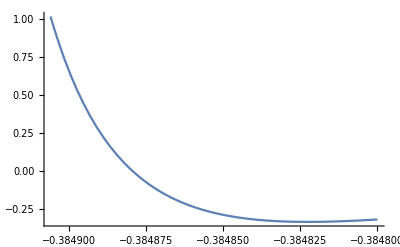

```mathematica
Plot[uu[x],{x,-0.3848,-0.384906}]
```

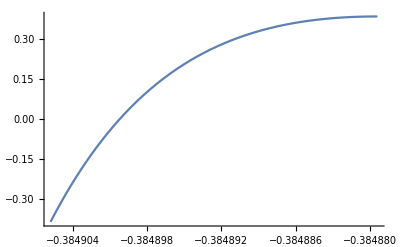

```mathematica
Plot[uup[x],{x,-0.384879389365321,-0.3849057861870625}]
```

```mathematica
uu[-0.384879389365321]
```

2.70716×10^-13

```mathematica
uu[-0.3849057861870625]-1
```

2.58726×10^-12

```mathematica
uup[-0.384879389365321]
```

0.384879

```mathematica
uup[-0.3849057861870625]
```

-0.384906

```mathematica
ku0=-0.384879389365321;
ku1=-0.3849057861870625;
```

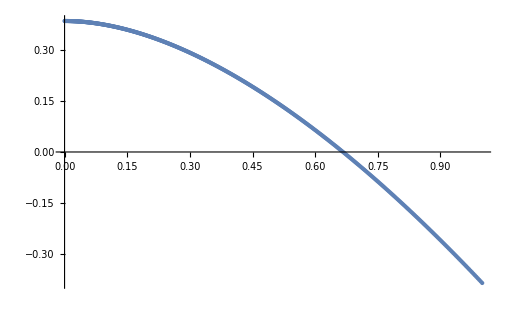

```mathematica
num=512;
uupUuTable=Table[0,{i,1,num}];
For[i=1,i<num+1,i++,
k=(ku0(num-i)+ku1(i-1))/(num-1);
uupUuTable[[i]]={uu[k],uup[k]}
]
ListPlot[uupUuTable,PlotRange->Full,PlotStyle->PointSize[Small]]
```

```mathematica
Subscript[ψ, 2][ahh_]:=If[ArcCot[uup[ahh]/(-uu[ahh] √(1-uu[ahh]))]<0,ArcCot[uup[ahh]/(-uu[ahh] √(1-uu[ahh]))]+π,ArcCot[uup[ahh]/(-uu[ahh] √(1-uu[ahh]))]]
```

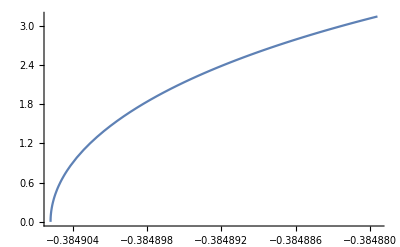

```mathematica
Plot[Subscript[ψ, 2][x],{x,ku1,ku0}]
```

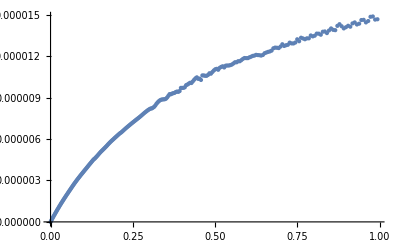

```mathematica
num=256;
psi2Table=Table[0,{i,1,num-1}];
For[i=1,i<num,i++,
k=(ku0(num-i)+ku1(i-1))/(num-1);
u0=uu[k];
psi2Table[[i]]={u0,1-(Subscript[ψ, 2][k])/(Subscript[ψ, m][u0])}
]
ListPlot[psi2Table,PlotRange->Full,PlotStyle->PointSize[Small]]
```

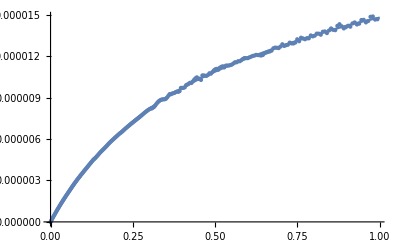

0.0000412057 x-0.0000596807 x^2+0.0000499505 x^3-0.0000166777 x^4

7.70683×10^-8

```mathematica
fitpsi2=Fit[psi2Table,{x,x^2,x^3,x^4},x];Show[ListPlot[psi2Table,PlotRange->Full,PlotStyle->PointSize[Small]],Plot[fitpsi2,{x,0,1}]]
fitpsi2
√((1/(num-1))Sum[(psi2Table[[i,2]]-fitpsi2/.x->psi2Table[[i,1]])^2,{i,1,num-1}])
```

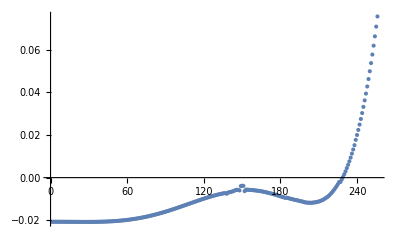

{{1,-0.0207029},{2,-0.0207032},{3,-0.0207038},{4,-0.0207048},{5,-0.0207066},{6,-0.0207084},{7,-0.0207107},{8,-0.0207133},{9,-0.0207162},{10,-0.0207194},{11,-0.0207228},{12,-0.0207263},{13,-0.0207303},{14,-0.0207344},{15,-0.0207385},{16,-0.0207428},{17,-0.020747},{18,-0.0207512},{19,-0.0207553},{20,-0.0207595},{21,-0.0207632},{22,-0.0207665},{23,-0.0207696},{24,-0.0207721},{25,-0.0207742},{26,-0.0207757},{27,-0.0207765},{28,-0.0207766},{29,-0.0207758},{30,-0.0207741},{31,-0.0207714},{32,-0.0207676},{33,-0.0207626},{34,-0.0207564},{35,-0.0207484},{36,-0.0207393},{37,-0.0207287},{38,-0.0207164},{39,-0.0207026},{40,-0.0206865},{41,-0.0206688},{42,-0.020649},{43,-0.0206271},{44,-0.020603},{45,-0.0205766},{46,-0.0205479},{47,-0.0205168},{48,-0.0204831},{49,-0.0204466},{50,-0.0204073},{51,-0.0203653},{52,-0.0203203},{53,-0.0202722},{54,-0.0202213},{55,-0.0201675},{56,-0.0201101},{57,-0.0200495},{58,-0.0199855},{59,-0.0199179},{60,-0.0198474},{61,-0.0197731},{62,-0.0196952},{63,-0.0196136},{64,-0.0195282},{65,-0.0194392},{66,-0.0193464},{67,-0.0192501},{68,-0.0191498},{69,-0.0190456},{70,-0.0189376},{71,-0.0188256},{72,-0.0187098},{73,-0.0185902},{74,-0.0184667},{75,-0.0183392},{76,-0.0182076},{77,-0.0180723},{78,-0.0179334},{79,-0.0177906},{80,-0.0176442},{81,-0.017494},{82,-0.0173402},{83,-0.0171831},{84,-0.0170227},{85,-0.0168582},{86,-0.0166902},{87,-0.0165192},{88,-0.0163512},{89,-0.016174},{90,-0.015993},{91,-0.0158039},{92,-0.0156231},{93,-0.0154342},{94,-0.0152371},{95,-0.0150431},{96,-0.0148469},{97,-0.0146483},{98,-0.0144478},{99,-0.0142454},{100,-0.014041},{101,-0.0138351},{102,-0.0136279},{103,-0.0134196},{104,-0.0132103},{105,-0.013},{106,-0.0127894},{107,-0.0125778},{108,-0.0123754},{109,-0.0121645},{110,-0.0119457},{111,-0.0117345},{112,-0.0115254},{113,-0.0113163},{114,-0.0111136},{115,-0.0109042},{116,-0.0106984},{117,-0.0104927},{118,-0.0102892},{119,-0.0100892},{120,-0.00989129},{121,-0.00969622},{122,-0.00950503},{123,-0.00931142},{124,-0.00912833},{125,-0.00895222},{126,-0.00877174},{127,-0.00860294},{128,-0.00843615},{129,-0.00827691},{130,-0.00811396},{131,-0.0079613},{132,-0.00781679},{133,-0.00768275},{134,-0.00753942},{135,-0.00743107},{136,-0.00730467},{137,-0.00729213},{138,-0.00754326},{139,-0.00702032},{140,-0.00686162},{141,-0.00670294},{142,-0.00656559},{143,-0.00635681},{144,-0.00611814},{145,-0.0058377},{146,-0.00569076},{147,-0.005803},{148,-0.00600118},{149,-0.00395953},{150,-0.00380813},{151,-0.00385958},{152,-0.00633991},{153,-0.00564642},{154,-0.00565763},{155,-0.00570922},{156,-0.00575378},{157,-0.00580349},{158,-0.00584433},{159,-0.00590633},{160,-0.00597563},{161,-0.00605247},{162,-0.00613148},{163,-0.00620362},{164,-0.00630299},{165,-0.00641013},{166,-0.00652474},{167,-0.00664623},{168,-0.00677474},{169,-0.00690969},{170,-0.00705103},{171,-0.00719889},{172,-0.00735296},{173,-0.00751244},{174,-0.00767703},{175,-0.00784675},{176,-0.00802076},{177,-0.00819892},{178,-0.00838268},{179,-0.00856732},{180,-0.00875422},{181,-0.00894252},{182,-0.00913158},{183,-0.00932064},{184,-0.00950846},{185,-0.00942215},{186,-0.00959442},{187,-0.00976291},{188,-0.00992622},{189,-0.0100829},{190,-0.0102323},{191,-0.0103752},{192,-0.0105094},{193,-0.0106369},{194,-0.0107657},{195,-0.0109534},{196,-0.011084},{197,-0.0112111},{198,-0.0113307},{199,-0.0115698},{200,-0.0116624},{201,-0.0117342},{202,-0.0117719},{203,-0.0117947},{204,-0.0118011},{205,-0.0117897},{206,-0.0116527},{207,-0.0116312},{208,-0.0115188},{209,-0.011379},{210,-0.0112097},{211,-0.011014},{212,-0.0107678},{213,-0.0104863},{214,-0.0101553},{215,-0.00977937},{216,-0.00938935},{217,-0.00899519},{218,-0.00845712},{219,-0.00786234},{220,-0.00721022},{221,-0.0065003},{222,-0.00573082},{223,-0.0049015},{224,-0.00401036},{225,-0.00305709},{226,-0.00203757},{227,-0.00205649},{228,-0.000921821},{229,0.000289576},{230,0.00158105},{231,0.00295382},{232,0.00447973},{233,0.00602453},{234,0.00766008},{235,0.00938951},{236,0.0112733},{237,0.013202},{238,0.0152346},{239,0.017738},{240,0.0200095},{241,0.022398},{242,0.0249075},{243,0.027542},{244,0.0303081},{245,0.0332116},{246,0.0362554},{247,0.0394444},{248,0.0427841},{249,0.04628},{250,0.0499379},{251,0.0537637},{252,0.0577636},{253,0.0619443},{254,0.0663141},{255,0.0708813},{256,0.0756514}}

```mathematica
num=256;
testResult=Table[0,{i,1,num}];
For[i=1,i<num+1,i++,
Clear[y];
u0=0.9999Cos[(π(i-1))/(2num)];
Subscript[ψ, mu]=N[Subscript[ψ, m][u0]];
Subscript[ψ, m2]=N[(1-fitpsi2/.x->u0)Subscript[ψ, mu]];
sol=NDSolve[{y''[x]+y[x]-3/2 y[x]^2==0,y[0]==u0,y'[0]==-u0 √(1-u0)Cot[Subscript[ψ, m2]]},y,{x,0,18}];

t=y/.sol[[1,1]];
testResult[[i]]={i,(x/.FindRoot[t[x],{x,4π-1}][[1]])-4π};
]
ListPlot[testResult,PlotRange->Full]
testResult
```

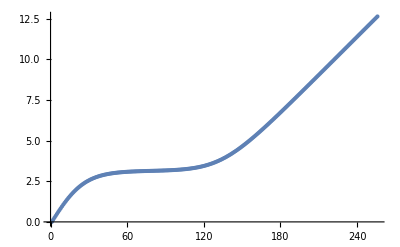

```mathematica
num=256;
u0=0.0001;
Subscript[ψ, mu]=N[Subscript[ψ, m][u0]];
athpsi2=ArcTanh[1-fitpsi2/.x->u0];
Subscript[ψ, m2]=N[(1-fitpsi2/.x->u0)Subscript[ψ, mu]];
testResult=Table[{i,0},{i,1,num}];
root=4 π/0.95;
For[i=num,i>1,i--,Clear[y];
sol=NDSolve[{y''[x]+y[x]-3/2 y[x]^2==0,y[0]==u0,y'[0]==-u0 √(1-u0)Cot[Tanh[athpsi2(i-1)/(num-1)] Subscript[ψ, mu]]},y,{x,0,18}];

t=y/.sol[[1,1]];
root=x/.FindRoot[t[x],{x,0.95root}][[1]];
testResult[[i]]={i,root};
]
ListPlot[testResult]
```

```mathematica
num0=256;
num1=256;
unifiedTable=Table[Table[0,{i,1,num1}],{j,1,num0}];
(*i从1到num0: u0从0.9999到0, Subscript[ψ, m] 从0到π*)
(*j从1到num1: Subscript[ψ从0到ψ, 2]*)
(*u0=0时可以直接令Δϕ=0,*)
For[i=1,i<num0,i++,
u0=0.9999Cos[(π(i-1))/(2(num0-1))];
Subscript[ψ, mu]=N[Subscript[ψ, m][u0]];
athpsi2=ArcTanh[1-fitpsi2/.x->u0];
root=4 π/0.95;
For[j=num1,j>1,j--,
sol=NDSolve[{y''[x]+y[x]-3/2 y[x]^2==0,y[0]==u0,y'[0]==-u0 √(1-u0)Cot[Tanh[athpsi2(j-1)/(num1-1)] Subscript[ψ, mu]]},y,{x,0,18}];
t=y/.sol[[1,1]];
root=x/.FindRoot[t[x],{x,0.95root}][[1]];
unifiedTable[[i,j]]=root;
]
]
Export["E:\\files\\C++\\BlackHoleRendering\\BlackHoleRendering\\BlackHoleRenderingNoneCuda\\resources\\unified_v2.0.txt",unifiedTable,"Table"];
unifiedTable
```

NDSolve::ndsz: At x == 17.9095, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At x == 17.8155, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At x == 17.7214, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

{1}
 |  |  |  |

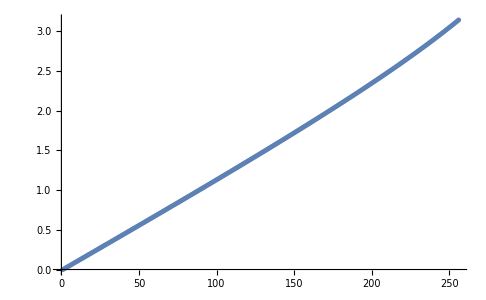

{0,0.0113166,0.0226333,0.0339501,0.045267,0.0565842,0.0679016,0.0792194,0.0905375,0.101856,0.113175,0.124495,0.135815,0.147136,0.158457,0.169779,0.181103,0.192427,0.203751,0.215077,0.226404,0.237732,0.249061,0.260391,0.271723,0.283056,0.29439,0.305725,0.317063,0.328401,0.339741,0.351083,0.362427,0.373772,0.385119,0.396468,0.407819,0.419172,0.430527,0.441884,0.453243,0.464604,0.475968,0.487334,0.498702,0.510073,0.521446,0.532822,0.544201,0.555582,0.566966,0.578353,0.589742,0.601135,0.612531,0.62393,0.635331,0.646737,0.658145,0.669557,0.680972,0.69239,0.703812,0.715238,0.726667,0.7381,0.749537,0.760978,0.772422,0.783871,0.795324,0.806781,0.818242,0.829707,0.841177,0.852651,0.86413,0.875613,0.887101,0.898594,0.910091,0.921594,0.933101,0.944614,0.956131,0.967654,0.979182,0.990715,1.00225,1.0138,1.02535,1.0369,1.04847,1.06003,1.07161,1.08319,1.09477,1.10636,1.11796,1.12957,1.14118,1.15279,1.16442,1.17605,1.18769,1.19933,1.21098,1.22264,1.23431,1.24598,1.25767,1.26935,1.28105,1.29276,1.30447,1.31619,1.32792,1.33965,1.3514,1.36315,1.37492,1.38669,1.39847,1.41026,1.42205,1.43386,1.44568,1.4575,1.46934,1.48118,1.49304,1.50491,1.51678,1.52867,1.54056,1.55247,1.56439,1.57632,1.58825,1.60021,1.61217,1.62414,1.63613,1.64812,1.66013,1.67215,1.68419,1.69623,1.70829,1.72036,1.73245,1.74454,1.75665,1.76878,1.78092,1.79307,1.80524,1.81742,1.82961,1.84182,1.85405,1.86629,1.87854,1.89081,1.9031,1.91541,1.92773,1.94006,1.95242,1.96479,1.97717,1.98958,2.002,2.01444,2.0269,2.03938,2.05188,2.0644,2.07694,2.08949,2.10207,2.11467,2.12729,2.13992,2.15259,2.16527,2.17797,2.1907,2.20345,2.21623,2.22902,2.24185,2.25469,2.26756,2.28046,2.29338,2.30633,2.31931,2.33231,2.34534,2.3584,2.37148,2.3846,2.39774,2.41092,2.42412,2.43736,2.45063,2.46393,2.47727,2.49063,2.50403,2.51747,2.53094,2.54445,2.558,2.57158,2.5852,2.59886,2.61256,2.6263,2.64008,2.65391,2.66778,2.68169,2.69565,2.70965,2.7237,2.7378,2.75195,2.76615,2.7804,2.7947,2.80906,2.82347,2.83793,2.85246,2.86704,2.88169,2.8964,2.91117,2.926,2.9409,2.95587,2.97091,2.98603,3.00121,3.01648,3.03182,3.04724,3.06274,3.07833,3.09401,3.10978,3.12564,3.14159}

```mathematica
num=256;
psimTable=Table[0,{i,1,num}];
For[i=2,i<num+1,i++,
Clear[y];
u0=N[Cos[(π(i-1))/(2(num-1))]];

Subscript[ψ, mu]=N[Subscript[ψ, m][u0]];
Subscript[ψ, m2]=N[(1-fitpsi2/.x->u0)Subscript[ψ, mu]];
athpsi2=ArcTanh[1-fitpsi2/.x->u0];
psimTable[[i]]=Subscript[ψ, mu];
]
psimTable[[1]]=0;
psimTable[[num]]=N[π];
ListPlot[psimTable,PlotRange->Full]
Export["E:\\files\\C++\\BlackHoleRendering\\BlackHoleRendering\\BlackHoleRenderingNoneCuda\\resources\\psim.txt",psimTable,"Table"];
psimTable
```